```mathematica
Import["ToMatlab.m"]
```

```mathematica
f[t_]=Exp[-(t+2)^2/Sqrt[2.]]+Exp[-(t-2)^2/Sqrt[2.]]
```

ⅇ^(-0.707107 (-2+t)^2)+ⅇ^(-0.707107 (2+t)^2)

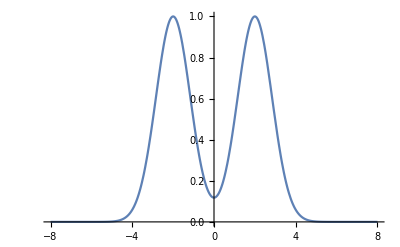

```mathematica
Plot[Evaluate[Abs[f[t]]],{t,-8,8}, PlotRange-> All]
```

```mathematica
K[k_,u_,aa_,bb_,dd_]=Exp[Pi*{k^2}*ⅈ*(aa/bb)]*Exp[-2*Pi*u*k*ⅈ*(1/bb)]*Exp[Pi*{u^2}*ⅈ*(dd/bb)]
```

{ⅇ^((ⅈ aa k^2 π)/bb-(2 ⅈ k π u)/bb+(ⅈ dd π u^2)/bb)}

```mathematica
a=1
b=3
d=1
c=(a*d-1)/b
```

1

3

1

0

```mathematica
fshift[t_,k_]=f[t-(k/2)]
Newfo[t_]=Simplify[Conjugate[f[t]], t∈Reals]
fconjshift[t_,k_]=Newfo[t+(k/2)]
ROFf[t_,k_]= Simplify[fshift[t,k]*fconjshift[t,k]]
```

ⅇ^(-0.707107 (-2-k/2+t)^2)+ⅇ^(-0.707107 (2-k/2+t)^2)

ⅇ^(-0.707107 (-2.+t)^2)+ⅇ^(-0.707107 (2+t)^2)

ⅇ^(-0.707107 (-2.+k/2+t)^2)+ⅇ^(-0.707107 (2+k/2+t)^2)

(ⅇ^(-0.176777 (-4.+k-2. t)^2)+ⅇ^(-0.176777 (4.+k-2. t)^2)) (ⅇ^(-0.176777 (-4.+k+2. t)^2)+ⅇ^(-0.176777 (4.+k+2. t)^2))

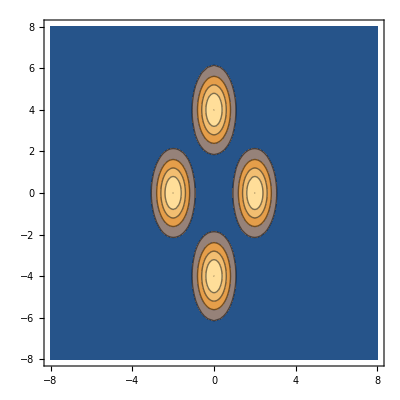

```mathematica
CPofOrg=ContourPlot[Evaluate[Abs[ROFf[t,k]]],{t,-8,8},{k,-8,8}, PlotRange-> All]
```

```mathematica
BDF1[t_,u_]=Simplify[Integrate[ROFf[t,k]*K[k,u,a,b,d],{k,-Infinity,Infinity}]]
```

{ⅇ^(-5.65685 t-1.41421 t^2-(0.317377-0.107152 ⅈ) u^2) ((0.00478467+0.00343461 ⅈ)+(0.00478467+0.00343461 ⅈ) ⅇ^(11.3137 t)-(0.0072859-0.00757059 ⅈ) ⅇ^(5.65685 t-(2.53901-0.857218 ⅈ) u)-(0.0072859-0.00757059 ⅈ) ⅇ^(5.65685 t+(2.53901-0.857218 ⅈ) u))}

```mathematica
a=ⅇ^(-5.65685424949238 t-1.414213562373095 t^2-(0.3173767761460979-0.1071523087251273 ⅈ) u^2) ((0.004784672605373991+0.0034346145050904546 ⅈ)+(0.004784672605373991+0.0034346145050904546 ⅈ) ⅇ^(11.31370849898476 t)-(0.007285898235138512-0.007570591702351853 ⅈ) ⅇ^(5.65685424949238 t-(2.5390142091687826-0.8572184698010199 ⅈ) u)-(0.007285898235138512-0.007570591702351853 ⅈ) ⅇ^(5.65685424949238 t+(2.5390142091687826-0.8572184698010199 ⅈ) u))
```

ⅇ^(-5.65685 t-1.41421 t^2-(0.317377-0.107152 ⅈ) u^2) ((0.00478467+0.00343461 ⅈ)+(0.00478467+0.00343461 ⅈ) ⅇ^(11.3137 t)-(0.0072859-0.00757059 ⅈ) ⅇ^(5.65685 t-(2.53901-0.857218 ⅈ) u)-(0.0072859-0.00757059 ⅈ) ⅇ^(5.65685 t+(2.53901-0.857218 ⅈ) u))

```mathematica
ToMatlab[a]
```

exp(1).^((-0.565685E1).*t+(-0.141421E1).*t.^2+((-0.317377E0)+sqrt( ...
  -1)*0.107152E0).*u.^2).*((0.478467E-2+sqrt(-1)*0.343461E-2)+( ...
  0.478467E-2+sqrt(-1)*0.343461E-2).*exp(1).^(0.113137E2.*t)+(( ...
  -0.72859E-2)+sqrt(-1)*0.757059E-2).*exp(1).^(0.565685E1.*t+(( ...
  -0.253901E1)+sqrt(-1)*0.857218E0).*u)+((-0.72859E-2)+sqrt(-1)* ...
  0.757059E-2).*exp(1).^(0.565685E1.*t+(0.253901E1+sqrt(-1)*( ...
  -0.857218E0)).*u));

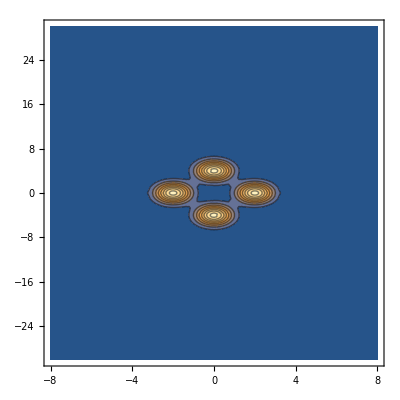

```mathematica
ContourPlot[Abs[BDF1[t,u]],{t,-8,8},{u,-30,30},PlotRange->All]
```

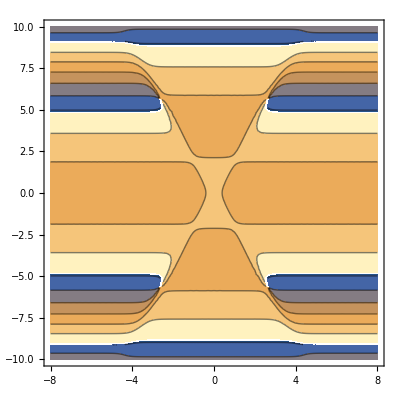

```mathematica
CPofBDF2=ContourPlot[Arg[BDF1[t,u]],{t,-8,8},{u,-10,10},PlotRange->All]
```